## Set Directory

```mathematica
pathtodirectory ="~/Desktop/";
```

```mathematica
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data/"];
```

## Style Settings

```mathematica
labelfont = "Arial";
Clear[x];
prediction[x_]:=-6.367767314992545+4.6042335007240975 √x;
```

```mathematica
redtoblue[z_]:= Blend[{RGBColor[1,0,0], RGBColor[0,0,1]}, z];
bluetored[z_] := Blend[{RGBColor[0,0,1], RGBColor[1,0,0]}, z];
```

```mathematica
thicknesstable = Table[{Directive[Thick, PointSize[Medium]], Directive[Thin], Directive[Thin]}];
thicknesslist = {Directive[Thick, PointSize[Medium]], Directive[Thick], Directive[Thick]};
```

## Figure 1 : Schematic

```mathematica
scale = 10;
```

```mathematica
fieldofview = {{-11*scale, 11*scale}, {-10*scale, 10*scale}};
```

```mathematica
contextcoord = {{1.75, 1}*scale, {1.75, -1}*scale};
graphics={Style["StyleBox[\"●\",FontSize->105]",Blue],Style["StyleBox[\"☺\",FontSize->110]",White],Style["StyleBox[\"○\",FontSize->115]",Blue], Style["StyleBox[\"○\",FontSize->100]",Blue]};
csmileycoord1 =ListPlot[{{contextcoord[[1]]}, {contextcoord[[1]]+{0,.085}},{contextcoord[[1]]},{contextcoord[[1]]}}, PlotRange -> fieldofview, PlotMarkers ->graphics, Axes -> None];
csmileycoord2 =ListPlot[{{contextcoord[[2]]}, {contextcoord[[2]]+{0,.085}},{contextcoord[[2]]}, {contextcoord[[2]]}}, PlotRange -> fieldofview, PlotMarkers ->graphics, Axes -> None];
circles1=Graphics[Table[Style[Disk[{contextcoord[[All,1]][[i]], contextcoord[[All, 2]][[i]]}, 2.75*scale], Blue, Opacity[.3]], {i, 1, 2}], PlotRange -> fieldofview, Ticks-> None];
contextalone=Show[circles1, csmileycoord1,csmileycoord2, ImageSize-> 900];
```

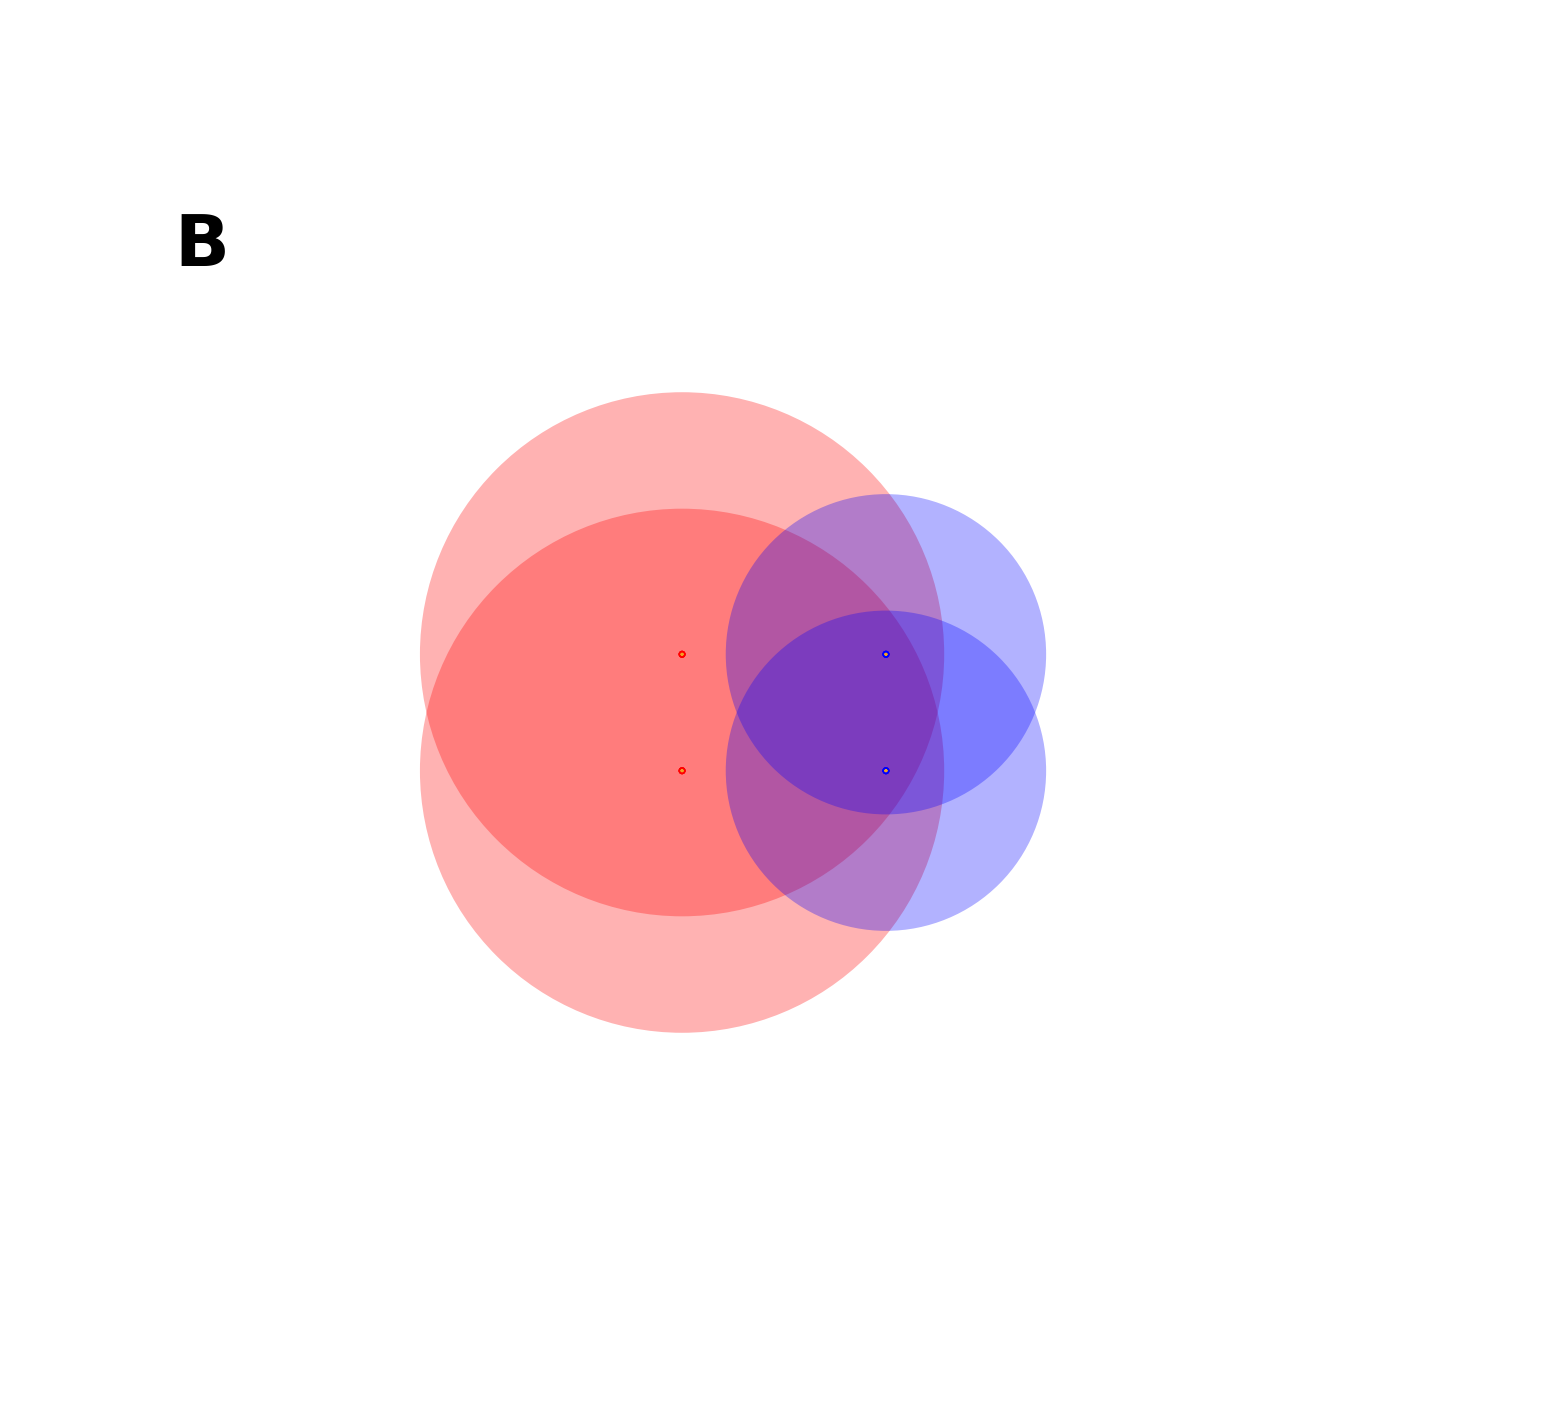

```mathematica
colors = {RGBColor[1,0,0], RGBColor[1,0,0]};
coords = {{-1.75, -1}*scale,{-1.75, 1}*scale};
graphics={Style["StyleBox[\"●\",FontSize->105]",Red],Style["StyleBox[\"☺\",FontSize->110]",White],Style["StyleBox[\"○\",FontSize->115]",Red], Style["StyleBox[\"○\",FontSize->100]",Red]};
stars1 =ListPlot[{{coords[[1]]}, {coords[[1]]+{0,.085}},{coords[[1]]},{coords[[1]]}}, PlotRange -> fieldofview, PlotMarkers ->graphics, Axes -> None];
stars2 =ListPlot[{{coords[[2]]}, {coords[[2]]+{0,.085}},{coords[[2]]}, {coords[[2]]}}, PlotRange -> fieldofview, PlotMarkers ->graphics, Axes -> None];
schematicthreshs = {4.5*scale, 4.5*scale};
circles = Graphics[Table[Style[Disk[{coords[[All,1]][[i]], coords[[All, 2]][[i]]}, schematicthreshs[[i]]], colors[[i]], Opacity[.3]], {i, 1, 2}], PlotRange -> fieldofview, Ticks-> None];
CFs = Show[circles, stars1,stars2,  ImageSize -> 2000,Epilog->{Text[Style["B",175,Bold,FontFamily->labelfont],Offset[{0,0},{-100,80}]]}];
p2=Show[CFs,contextalone]
```

```mathematica
contextcoord = {{4, 3}*scale, {4, -3}*scale};
graphics={Style["StyleBox[\"●\",FontSize->105]",Blue],Style["StyleBox[\"☺\",FontSize->110]",White],Style["StyleBox[\"○\",FontSize->115]",Blue],Style["StyleBox[\"○\",FontSize->100]",Blue]};
csmileycoord1 =ListPlot[{{contextcoord[[1]]}, {contextcoord[[1]]+{0,.085}},{contextcoord[[1]]},{contextcoord[[1]]}}, PlotRange -> fieldofview, PlotMarkers ->graphics, Axes -> None];
csmileycoord2 =ListPlot[{{contextcoord[[2]]}, {contextcoord[[2]]+{0,.085}},{contextcoord[[2]]}, {contextcoord[[2]]}}, PlotRange -> fieldofview, PlotMarkers ->graphics, Axes -> None];
circles1=Graphics[Table[Style[Disk[{contextcoord[[All,1]][[i]], contextcoord[[All, 2]][[i]]}, 6.75*scale], Blue, Opacity[.3]], {i, 1, 2}], PlotRange -> fieldofview, Ticks-> None];
contextalone=Show[circles1, csmileycoord1,csmileycoord2, ImageSize-> 900];
```

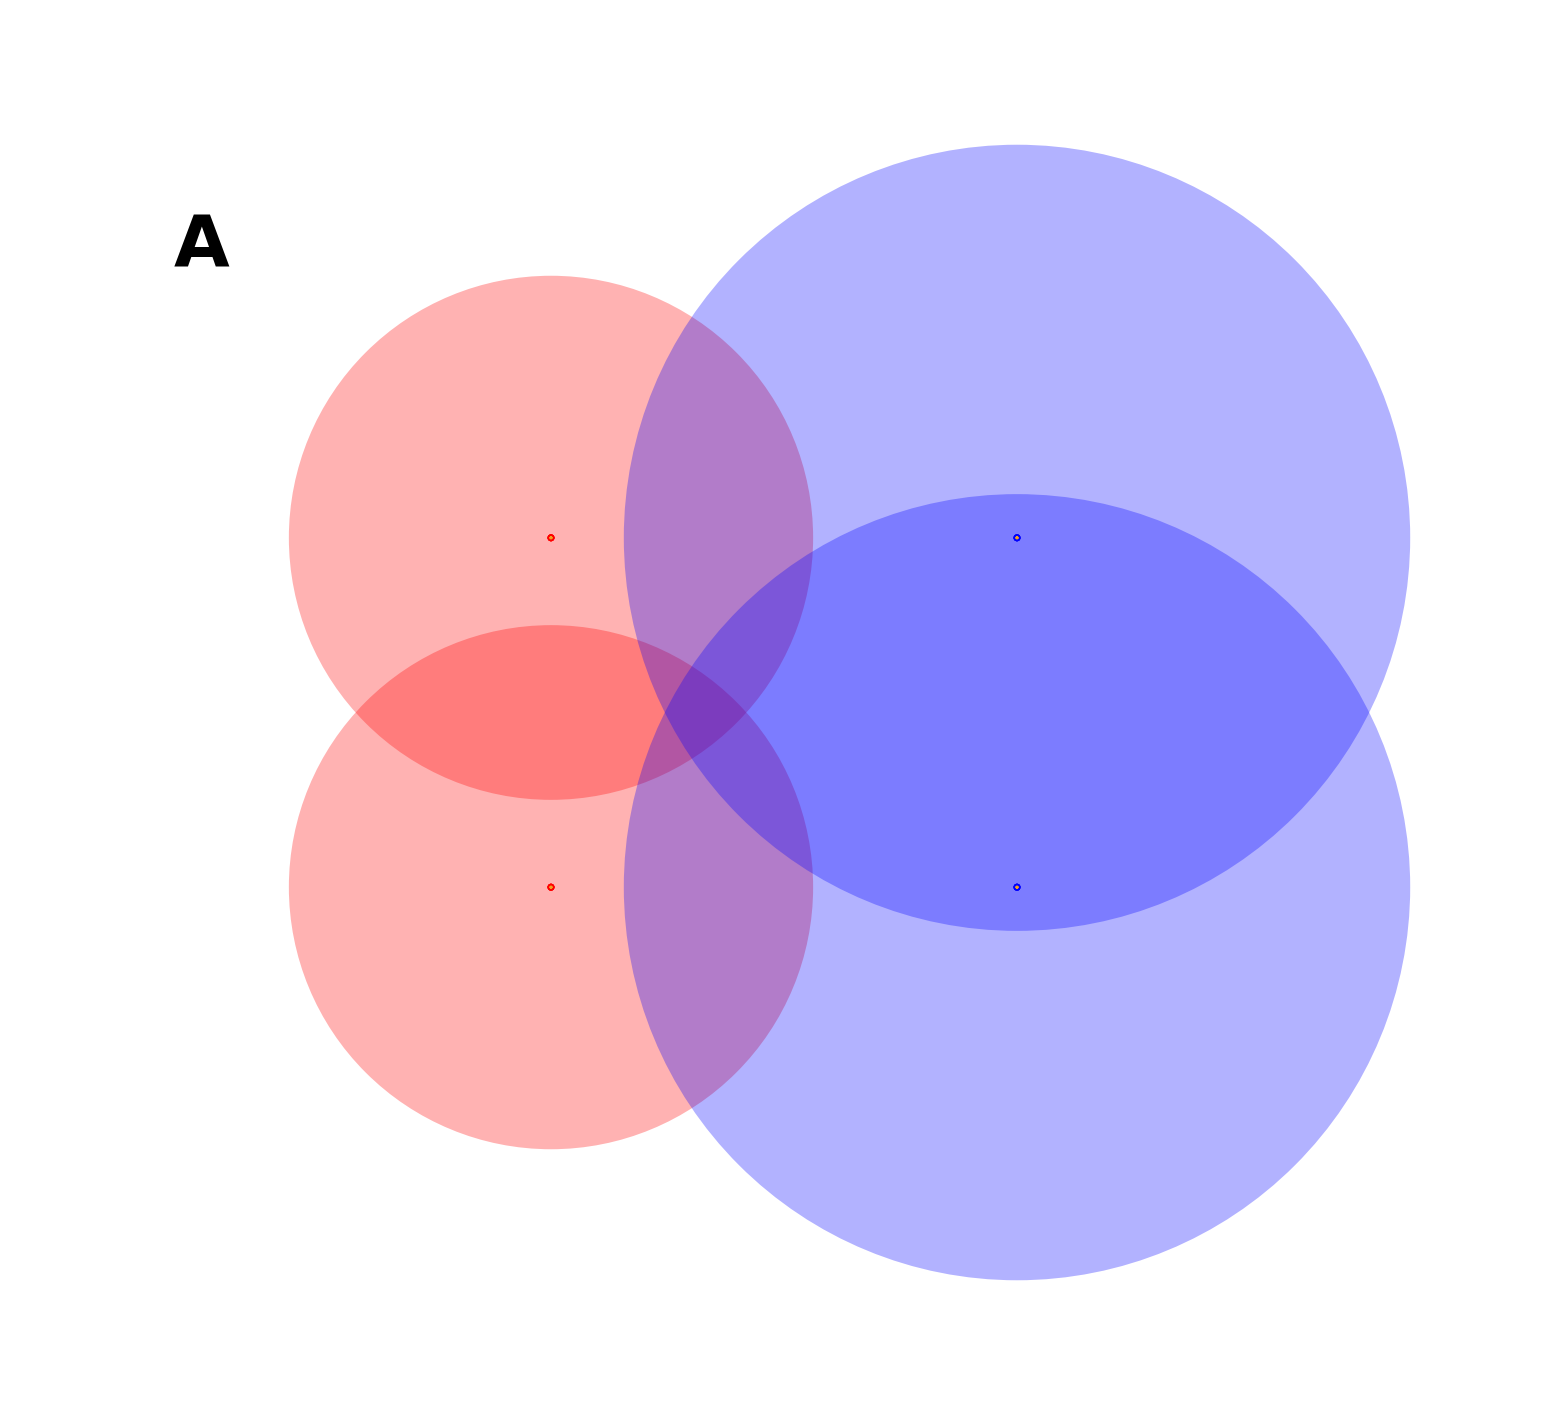

```mathematica
colors = {RGBColor[1,0,0], RGBColor[1,0,0]};
coords = {{-4, -3}*scale,{-4, 3}*scale};
graphics={Style["StyleBox[\"●\",FontSize->105]",Red],Style["StyleBox[\"☺\",FontSize->110]",White],Style["StyleBox[\"○\",FontSize->115]",Red], Style["StyleBox[\"○\",FontSize->100]",Red]};
stars1 =ListPlot[{{coords[[1]]}, {coords[[1]]+{0,.085}},{coords[[1]]},{coords[[1]]}}, PlotRange -> fieldofview, PlotMarkers ->graphics, Axes -> None];
stars2 =ListPlot[{{coords[[2]]}, {coords[[2]]+{0,.085}},{coords[[2]]}, {coords[[2]]}}, PlotRange -> fieldofview, PlotMarkers ->graphics, Axes -> None];
schematicthreshs = {4.5*scale, 4.5*scale};
circles = Graphics[Table[Style[Disk[{coords[[All,1]][[i]], coords[[All, 2]][[i]]}, schematicthreshs[[i]]], colors[[i]], Opacity[.3]], {i, 1, 2}], PlotRange -> fieldofview, Ticks-> None];
CFs = Show[circles, stars1,stars2,  ImageSize -> 2000,Epilog->{Text[Style["A",175,Bold,FontFamily->labelfont],Offset[{0,0},{-100,80}]]}];
p1=Show[CFs,contextalone]
```

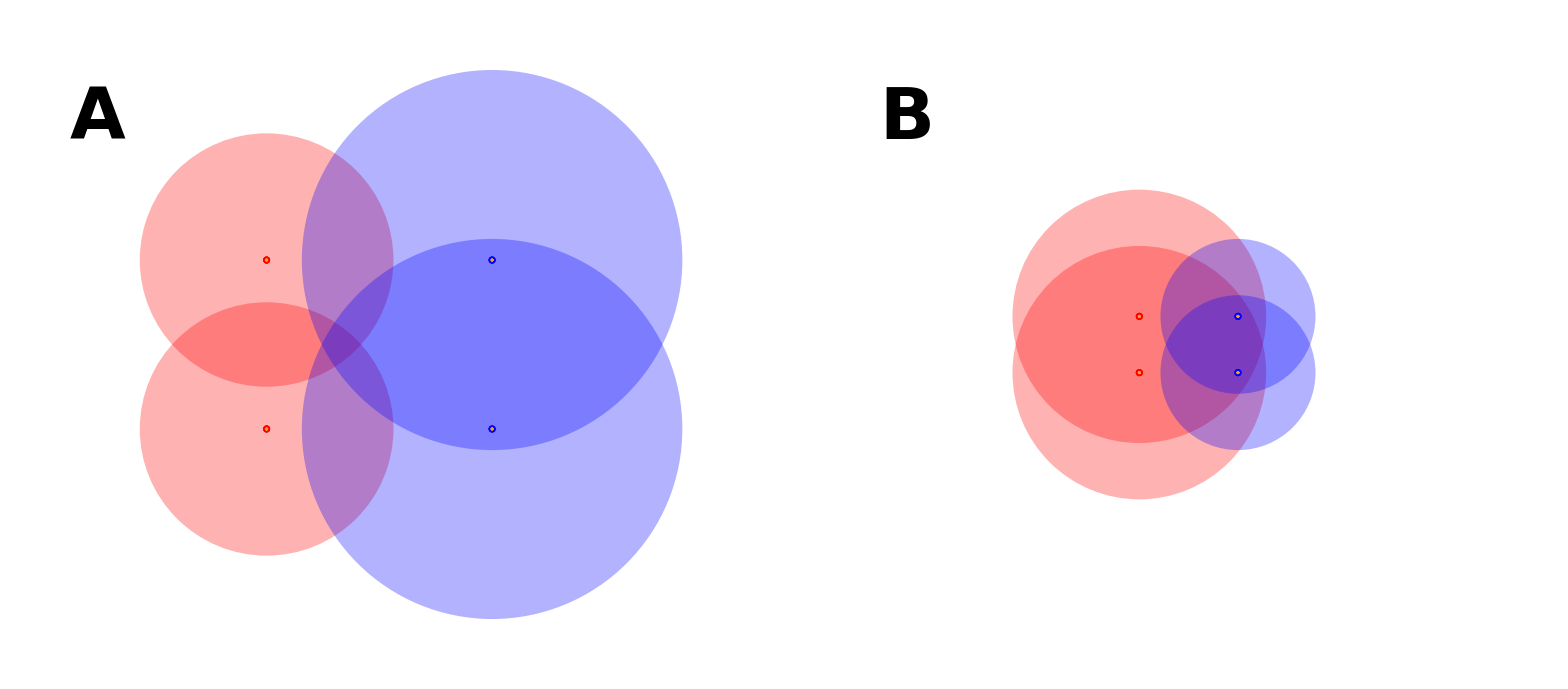

```mathematica
schem = GraphicsRow[{p1, p2}, ImageSize->5000]
```

```mathematica
currentdir=Directory[];
SetDirectory["~/Desktop"];
Export["schematic.pdf", schem];
SetDirectory[currentdir];
```

## Figure 2 : Time Series

```mathematica
fig2legend=SwatchLegend[{RGBColor[1,0,0], RGBColor[0,0,1]}, {"Innate","Plastic"},LegendMarkerSize->22,LabelStyle->Directive[Bold, Medium,22]];
```

```mathematica
totalscalerfreq=Import["fig2_plastic_frequencies.txt","CSV"];
```

### Frequency Plot

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data/"];
totalscalerfreq=Import["fig2_plastic_frequencies.txt","CSV"];
totalscalerfreq=Transpose[{Flatten[Downsample[totalscalerfreq, 2]], Flatten[Downsample[Drop[totalscalerfreq, 1], 2]]}];
SetDirectory[currentdir];
```

```mathematica
zeroes = Table[0, {i, 1, Length[totalscalerfreq[[All,1]]]}];
```

```mathematica
blue= Legended[ListPlot[{zeroes,totalscalerfreq[[All,2]]},LabelStyle -> {Bold},Joined-> True,PlotStyle->
Table[{Directive[Blue],thicknesslist[[i]]}, {i, 2, 3}], Filling -> {1-> {2}},AxesStyle->Directive[Black,Bold, 15],TicksStyle -> Directive[Black, Thick, 22,FontFamily->labelfont], FrameStyle->Directive[Black, Thick, 15], ImageSize->600], Placed[fig2legend, {.875, .7}]];
```

```mathematica
ones = Table[1000, {i, 1, Length[totalscalerfreq[[All,1]]]}];
```

```mathematica
red=ListPlot[{totalscalerfreq[[All,2]],ones},Joined-> True,LabelStyle -> {FontFamily->labelfont,Black,Large, 25,Bold},PlotStyle->
Table[{Directive[Red],thicknesstable[[i]]}, {i, 2, 3}],Filling -> {1-> {2}},FrameTicks ->{{0,2000, 4000, 6000,8000,10000 }, {{250,0.25},{500,0.5},{750,0.75},{1000,1.0}}},AxesStyle->Directive[Black,Bold, 15],TicksStyle -> Directive[Black, Thick, 25,FontFamily->labelfont], FrameStyle->Directive[Black, Thick, 22],AspectRatio->2.5/6, ImageSize -> 800,Epilog -> Text[Style[A,30,Bold,FontFamily-> labelfont],Offset[{0,0},{-2100,1025}]], PlotRangeClipping->False, ImagePadding->{{150,40},{25,5}},Frame-> True,FrameLabel->{"Threshold coefficient","Frequency"}, 
RotateLabel->True,FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Directive[FontOpacity->0,FontSize->0]}}];
```

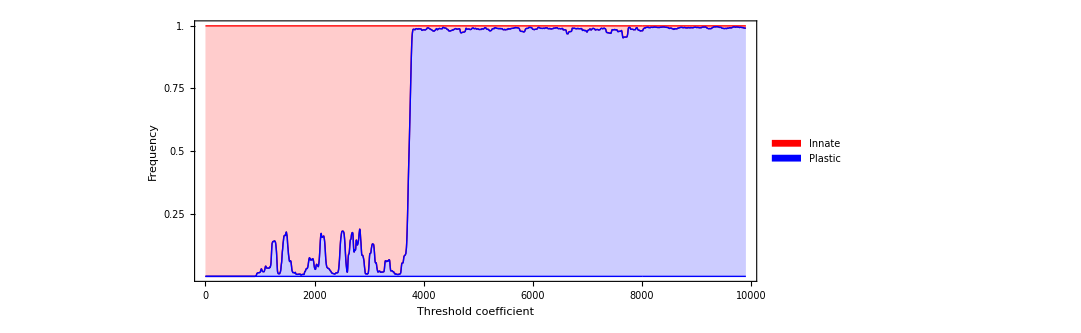

```mathematica
freqplot=Show[red, blue]
```

### Donation Rate Plot

#### Neutral donation rate

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/large_unprocessed_data"];
```

```mathematica
stat =Import["Context_STATISTICS_Dim020_Pop1000_Gen10000_B10.00_C1.00_PM1.0000_SM0.0000_ICthresh14.22300_ICscaler0.50000_Tsigma0.50000_Ssigma0.01000_invadingscaler0.00000_iteration2"];
times = Drop[stat[[All,1]],1];
```

```mathematica
donations = Drop[stat[[All,10]], 1];
```

```mathematica
donpts=Table[{i,donations[[i]]}, {i, 1, Length[donations],50}];
donptslist ={#} &/@donpts;
donstyle1 = Table[{redtoblue[Drop[stat[[All,5]],1][[i]]/1000]}, {i, 1, Length[donations],50}];
```

```mathematica
neutraldonptslist = donptslist;
averageneutraldons=N[Mean[Drop[Flatten[neutraldonptslist,1][[All,2]],1]]];
```

```mathematica
averageneutraldons
```

61.3116

```mathematica
averageneutraldons=61.311557788944725;
```

#### Donation data

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data/"];
donations=Flatten[Import["fig2_donations.txt","CSV"],1];
plasticfreqs=Flatten[Import["fig2_plastic_frequencies_unsmoothed.txt","CSV"],1];
SetDirectory[currentdir];
```

```mathematica
donpts=Table[{i,donations[[i]]}, {i, 1, Length[donations],50}];
donptslist ={#} &/@donpts;
donstyle1 = Table[{redtoblue[plasticfreqs[[i]]/1000]}, {i, 1, Length[plasticfreqs],50}];
```

```mathematica
r=redtoblue/@Flatten[plasticfreqs];
```

#### Generate donation figure

```mathematica
plotrangemax=5500;
```

```mathematica
poss=Flatten[Position[donpts[[All,2]],_?(#<plotrangemax&)]];
```

```mathematica
donptslist ={#} &/@donpts[[poss]];
donstyle1 = donstyle1[[poss]];
```

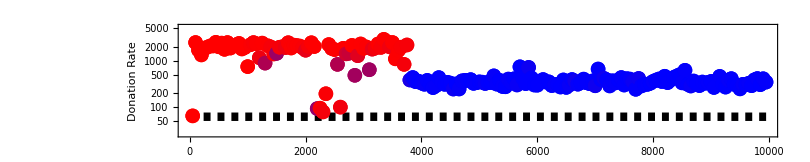

```mathematica
dons =Show[ListLogPlot[donptslist,PlotStyle-> donstyle1,PlotMarkers -> {"●",15},LabelStyle -> {FontFamily->labelfont,Black,Large, 25,Bold},PlotRange->{All,{25, 5500}},FrameTicks ->{{0,2000, 4000, 6000,8000,10000 }, {0,{50,"0.5%"},{500, "5%"},{2000,"20%"}}},AxesStyle->Directive[Black,Bold, 20],TicksStyle -> Directive[Black, Thick, 20,FontFamily->labelfont], FrameStyle->Directive[Black, Thick, 20],AspectRatio->1.2/6, ImageSize -> 810,Epilog -> Text[Style[B,27,Bold,FontFamily-> labelfont],Offset[{0,0},{-2100,9}]], PlotRangeClipping->False, ImagePadding->{{150,50},{25,25}},Frame-> True,FrameLabel->{"Threshold coefficient",Column[{"Donation", "Rate"},Center]}, 
RotateLabel->True,FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Directive[FontOpacity->0,FontSize->0]}}], Graphics[{Thickness[0.0075],Dashed, Black, Line[{{0, Log[averageneutraldons]}, {10000, Log[averageneutraldons]}}]}]]
```

### Phenotype Standard Deviation Plot

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data/"];
totalstddevs=Flatten[Import["fig2_total_pstd.txt","CSV"],1];
SetDirectory[currentdir];
```

```mathematica
stdpts=Table[{i,totalstddevs[[i]]}, {i, 1, Length[totalstddevs],50}];stdptslist ={#} &/@stdpts;
stdstyle1 = Table[{redtoblue[plasticfreqs[[i]]/1000]}, {i, 1, Length[plasticfreqs],50}];
```

```mathematica
plotrangemax=120;
```

```mathematica
poss=Flatten[Position[stdpts[[All,2]],_?(#<plotrangemax&)]];
```

```mathematica
stdptslist ={#} &/@stdpts[[poss]];
stdstyle1 = stdstyle1[[poss]];
```

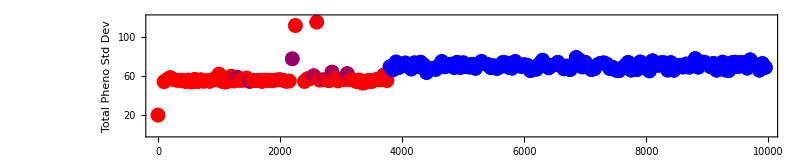

```mathematica
stds=ListPlot[stdptslist,PlotStyle-> stdstyle1,PlotMarkers -> {"●",15},PlotRange->{All,{0,120}},LabelStyle -> {FontFamily->labelfont,Black,Large, 25,Bold},
FrameTicks ->{{0,2000, 4000, 6000,8000,10000 },{20, 40, 60, 80, 100, 120}},AxesStyle->Directive[Black,Bold, 20],TicksStyle -> Directive[Black, Thick, 20,FontFamily->labelfont], FrameStyle->Directive[Black, Thick, 20],AspectRatio->1.2/6, ImageSize -> 810,Epilog -> Text[Style[C,27,Bold,FontFamily-> labelfont],Offset[{0,0},{-2100,120}]], PlotRangeClipping->False, ImagePadding->{{150,50},{35,31}},Frame-> True,FrameLabel->{"Threshold coefficient",Column[{"Total","Pheno Std Dev"},Center]}, 
RotateLabel->True,FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Directive[FontOpacity->0,FontSize->0]}}]
```

### Threshold Plot

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data/"];
dptslist=Flatten[Import["fig2_plastic_thresh_value.txt","CSV"],1];
dptslist=Transpose[{Flatten[Downsample[dptslist, 2]], Flatten[Downsample[Drop[dptslist, 1], 2]]}];
dptslist ={#} &/@dptslist;
dstyle=Flatten[Import["fig2_plastic_thresh_plotopacity.txt","CSV"],1];
dstyle1 = Table[{Opacity[dstyle[[i]]],Blue}, {i, 1, Length[dstyle],1}];
SetDirectory[currentdir];
```

```mathematica
plastic=ListPlot[dptslist,PlotStyle-> dstyle1,PlotMarkers -> {"●",15},PlotRange->{All,{0, 25}},Ticks ->{{0,2000, 4000, 6000,8000,10000 }, {0,5, 10, 15,20 , 25}},AxesStyle->Directive[Black,Bold, 15],TicksStyle -> Directive[Black, Thick, 18,FontFamily->labelfont], FrameStyle->Directive[Black, Thick, 15],AspectRatio->1/5, ImageSize -> 800];
```

```mathematica
currentdir=Directory[];
SetDirectory["~/Desktop/altruism_2_repo/data/"];
tptslist=Flatten[Import["fig2_innate_thresh_value.txt","CSV"],1];
tptslist=Transpose[{Flatten[Downsample[tptslist, 2]], Flatten[Downsample[Drop[tptslist, 1], 2]]}];
tptslist ={#} &/@tptslist;
tstyle=Flatten[Import["fig2_innate_thresh_plotopacity.txt","CSV"],1];
tstyle1 = Table[{Opacity[tstyle[[i]]],Red}, {i, 1, Length[tstyle],1}];
SetDirectory[currentdir];
```

```mathematica
thresh=ListPlot[tptslist,PlotStyle-> tstyle1,PlotMarkers -> {"●",15},PlotRange->{All,{0, 25}},Ticks ->{{0,2000, 4000, 6000,8000,10000 }, {0,5.0, 10.0, 15.0, 20.0, 25.0}},LabelStyle -> {FontFamily->labelfont,Black,Large, 25,Bold},AxesStyle->Directive[Black,Bold, 15],TicksStyle -> Directive[Black, Thick, 25,FontFamily->labelfont], FrameStyle->Directive[Black, Thick, 22],AspectRatio->1/6, ImageSize -> 810,Epilog -> Text[Style[D,27,Bold,FontFamily-> labelfont],Offset[{0,0},{-2100,25}]], PlotRangeClipping->False, ImagePadding->{{150,50},{65,25}},Frame-> True,FrameLabel->{"Generations","Threshold"}, 
RotateLabel->True,FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Directive[FontOpacity->0,FontSize->0]}}];
```

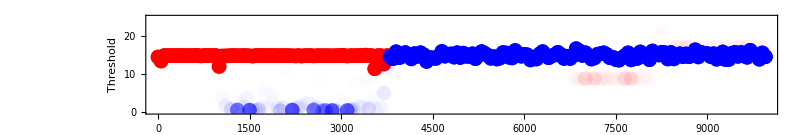

```mathematica
threshp=Show[thresh,plastic]
```

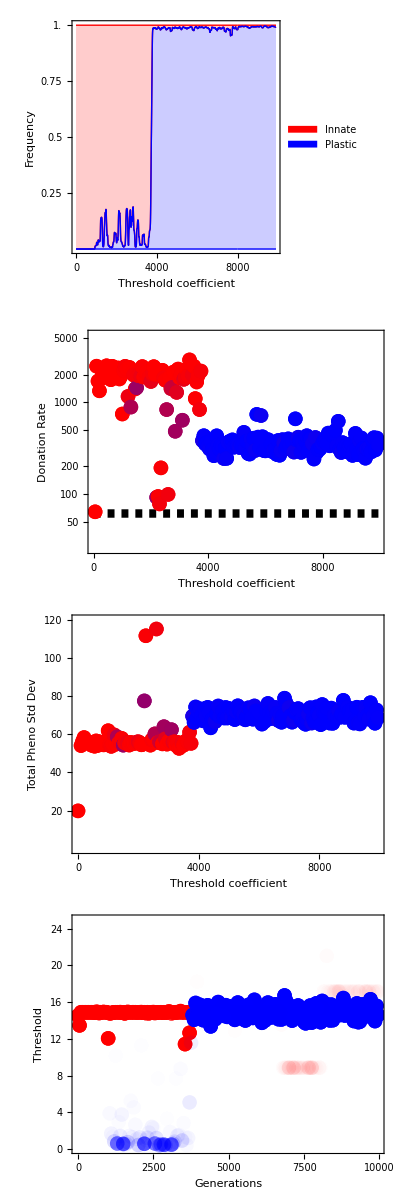

```mathematica
columned=Column[{freqplot, dons,stds, threshp}]
```

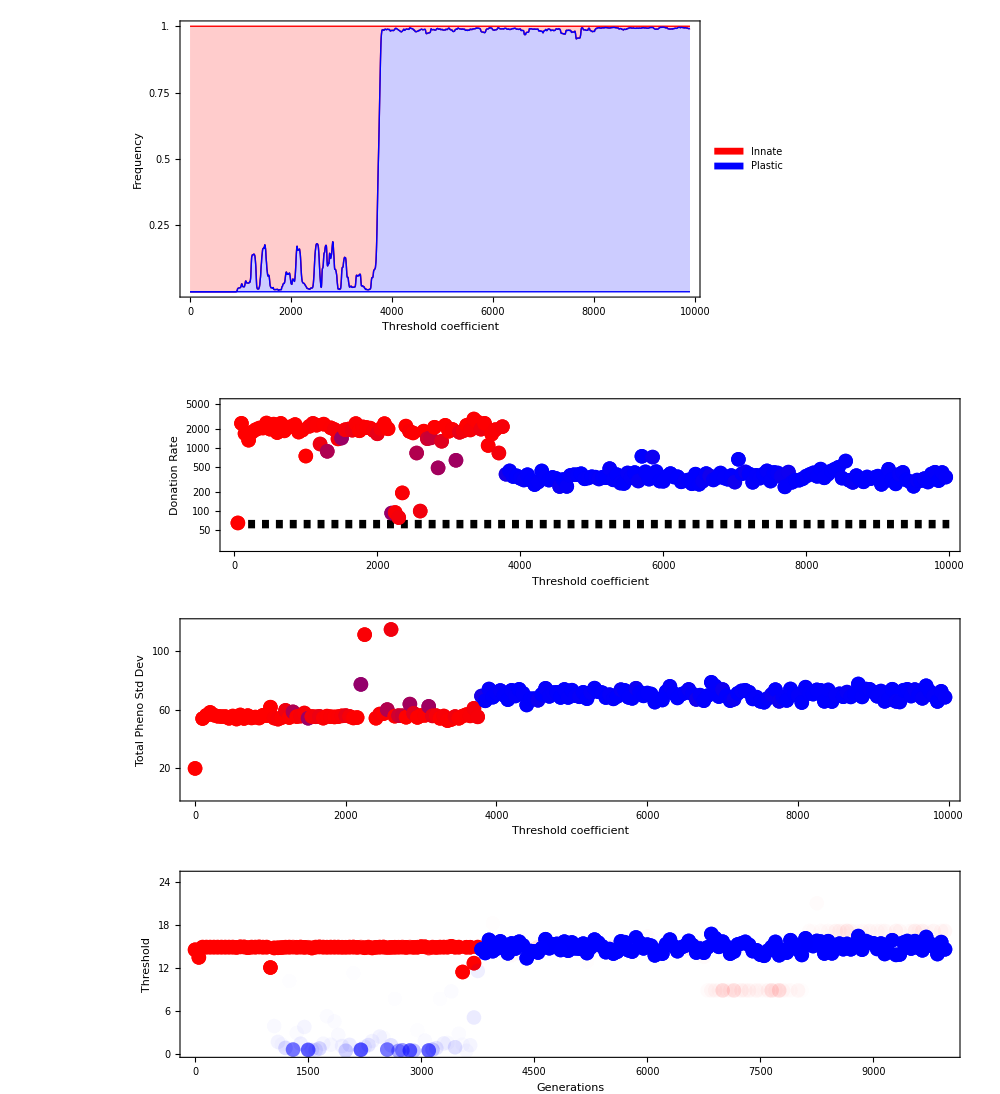

```mathematica
trial=GraphicsGrid[{{freqplot}, {dons},{stds}, {threshp}}, ImageSize->1000]
```

```mathematica
currentdir=Directory[];
SetDirectory["~/Desktop"];
Export["fig2.pdf", columned];
SetDirectory[currentdir];
```

## Figure 3 : Optimal Thresh Fig

### Params

```mathematica
redtowhite[z_]:= Blend[{RGBColor[1,0,0],RGBColor[1,.9,.9]}, z]
whitetoblue[z_]:= Blend[{RGBColor[1,1,1],RGBColor[0,0,1]}, z]
```

```mathematica
lowval = 150;
highval = 850;
```

```mathematica
maxdist = 50;
maxT = 50;
partitiongrid = 50;
```

### First look at Innates

```mathematica
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
```

```mathematica
totalscalerfreq=Import["fig3_all_runs_innate_fitnesses.txt","CSV"];
```

```mathematica
totalscalerfreq=Transpose[{Flatten[Downsample[totalscalerfreq, 3]], Flatten[Downsample[Drop[totalscalerfreq, 1], 3]],Flatten[Downsample[Drop[totalscalerfreq, 2], 3]]}];
```

```mathematica
flattened=totalscalerfreq;
```

```mathematica
list=Sort[flattened, #1[[1]]<#2[[1]]&];
partitions=BinCounts[list[[All,1]],maxdist/partitiongrid];
binnedcoords=TakeList[list,partitions];
```

```mathematica
binnedsublists = {};
For[i = 1, i ≤ Length[binnedcoords], i++,
list=Sort[binnedcoords[[i]], #1[[2]]<#2[[2]]&];
If[list ≠ {},
partitions=BinCounts[list[[All,2]],maxT/partitiongrid];
AppendTo[binnedsublists,TakeList[list,partitions]];
];
];
```

```mathematica
totaldeltaPinnate={};
min=5;
max=50;

For[i = 1, i <= Length[binnedsublists],i++,
For[j = 1, j<= Length[binnedsublists[[i]]],j++,
If[binnedsublists[[i]][[j]] != {},
If[Floor[binnedsublists[[i]][[j]][[1]][[1]]] <= max &&Floor[binnedsublists[[i]][[j]][[1]][[1]]] >= min,
AppendTo[totaldeltaPinnate, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Total[binnedsublists[[i]][[j]][[All,3]]]}];
];
]
]
];

maxbefore=Max[totaldeltaPinnate[[All,3]]];
minbefore=Min[totaldeltaPinnate[[All,3]]];

If[minbefore !=maxbefore,
mindensityb=minbefore;
maxdensityb=maxbefore;,
mindensityb = -1;
maxdensityb = 1;
];

If[maxdensityb==0,
maxdensityb=1;
,
];

xinnate=0.05*maxdensityb;

piece1b[x_]:=-1/mindensityb*x;
piece2b[x_]:=1/maxdensityb*x;
pwb[x_]:=Piecewise[{{piece1b[x], x < 0},{piece2b[x], x >=0} }];

delta=.05;

underlyingcolorbefore[z_]:=Map[Piecewise,{Join[Table[{redtowhite[i],-1+i<=z<-1+(i+delta)},{i, 0, 1-delta*2,delta}],
{{RGBColor[1,1,1],(-delta)<=z≤(delta)}},
Table[{whitetoblue[i],i<=z<(i+delta)},{i, delta, 1-delta,delta}],{{RGBColor[0,0,1],1<=z<100}}]}];

colordensityfunctionbefore[x_]:= underlyingcolorbefore[pwb[x]];

(*underlyingcolor[0.05] = min, so when pwb > 0.05.
this means 1/maxdensity*x = 0.05 => x = 1.1069476658333333
this amounts to a change in {RGBColor[1,1,1],(-delta)<=z≤(delta)} so that the upper bound is changed... but this will depend on the maxdensityb *)

plotlegendbefore=BarLegend[{colordensityfunctionbefore,{mindensityb,maxdensityb}},LegendLabel->"Δ P", LabelStyle->Directive[Bold, Medium, Black,15]];

transformedcolorbefore=Table[underlyingcolorbefore[pwb[totaldeltaPinnate[[i]][[3]]]],{i, 1, Length[totaldeltaPinnate[[All,3]]]}];
```

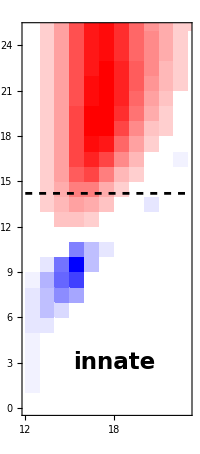

```mathematica
innateplot=Show[ Graphics[Table[Style[Rectangle[{totaldeltaPinnate[[i]][[1]],totaldeltaPinnate[[i]][[2]]},{totaldeltaPinnate[[i]][[1]]+50/partitiongrid,totaldeltaPinnate[[i]][[2]]+50/partitiongrid}], transformedcolorbefore[[i]], Opacity[1]], {i, 1, Length[totaldeltaPinnate[[All,3]]]}], PlotRange->{{12, 23}, {0, 25}}, Ticks-> None,Frame->True, FrameStyle->Directive[Black, Thick,Bold, 15],Epilog->Text[Style["innate", 23, Bold], Offset[{0,0}, {18,3}]],PlotRangeClipping->True],ListPlot[Table[{x,14.2},{x,12, 23}], Joined->True,PlotStyle->{Black, Dashed}]]
```

### Generate plastic figure

```mathematica
totalscalerfreq=Import["fig3_all_runs_plastic_fitnesses.txt","CSV"];
```

```mathematica
totalscalerfreq=Transpose[{Flatten[Downsample[totalscalerfreq, 3]], Flatten[Downsample[Drop[totalscalerfreq, 1], 3]],Flatten[Downsample[Drop[totalscalerfreq, 2], 3]]}];
```

```mathematica
flattened=totalscalerfreq;
```

```mathematica
list=Sort[flattened, #1[[1]]<#2[[1]]&];
partitions=BinCounts[list[[All,1]],maxdist/partitiongrid];
binnedcoords=TakeList[list,partitions];
```

```mathematica
binnedsublists = {};
For[i = 1, i ≤ Length[binnedcoords], i++,
list=Sort[binnedcoords[[i]], #1[[2]]<#2[[2]]&];
If[list ≠ {},
partitions=BinCounts[list[[All,2]],maxT/partitiongrid];
AppendTo[binnedsublists,TakeList[list,partitions]];
];
];
```

```mathematica
totaldeltaPplastic={};
min=5;
max=50;

For[i = 1, i <= Length[binnedsublists],i++,
For[j = 1, j<= Length[binnedsublists[[i]]],j++,
If[binnedsublists[[i]][[j]] != {},
If[Floor[binnedsublists[[i]][[j]][[1]][[1]]] <= max &&Floor[binnedsublists[[i]][[j]][[1]][[1]]] >= min,
AppendTo[totaldeltaPplastic, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Total[binnedsublists[[i]][[j]][[All,3]]]}];
];
]
]
];

If[maxbefore<Max[totaldeltaPplastic[[All,3]]],
maxbefore=Max[totaldeltaPplastic[[All,3]]]];

If[minbefore>Min[totaldeltaPplastic[[All,3]]],
minbefore=Min[totaldeltaPplastic[[All,3]]];
]

If[minbefore !=maxbefore,
mindensityb=minbefore;
maxdensityb=maxbefore;,
mindensityb = -1;
maxdensityb = 1;
];

If[maxdensityb==0,
maxdensityb=1;
,
];

piece1b[x_]:=-1/mindensityb*x;
piece2b[x_]:=1/maxdensityb*x;
pwb[x_]:=Piecewise[{{piece1b[x], x < 0},{piece2b[x], x >=0} }];

delta=.05;

upperbound = 1.1;

innatepos = 1/maxdensityb*xinnate;
innatepos *=1;
underlyingcolorbefore[z_]:=Map[Piecewise,{Join[Table[{redtowhite[i],-1+i<=z<-1+(i+delta)},{i, 0, 1-delta*2,delta}],
{{RGBColor[1,1,1],(-delta)<=z<innatepos}},{{whitetoblue[delta],innatepos<=z<delta}},
Table[{whitetoblue[i+delta],i<=z<(i+delta)},{i, delta, 1-delta,delta}],{{RGBColor[0,0,1],1<=z<upperbound}}]}];

colordensityfunctionbefore[x_]:= underlyingcolorbefore[pwb[x]];

plotlegendbefore=BarLegend[{colordensityfunctionbefore,{mindensityb,maxdensityb}},LegendLabel->"Δ P", LabelStyle->Directive[Bold, Medium, Black,15]];

transformedcolorbefore=Table[underlyingcolorbefore[pwb[totaldeltaPplastic[[i]][[3]]]],{i, 1, Length[totaldeltaPplastic[[All,3]]]}];
```

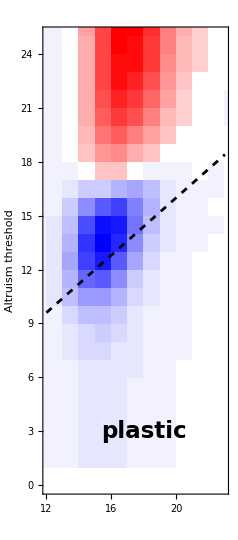

```mathematica
plasticplot=Show[ Graphics[Table[Style[Rectangle[{totaldeltaPplastic[[i]][[1]],totaldeltaPplastic[[i]][[2]]},{totaldeltaPplastic[[i]][[1]]+50/partitiongrid,totaldeltaPplastic[[i]][[2]]+50/partitiongrid}], transformedcolorbefore[[i]], Opacity[1]], {i, 1, Length[totaldeltaPplastic[[All,3]]]}], (*PlotRange -> {{10, 35}, {0, 55}},*)PlotRange->{{12, 23}, {0, 25}}, Ticks-> None,Frame->True, FrameTicksStyle->Directive[Black, Thick,Bold, 15],FrameStyle->Directive[Black, Thick,Bold, 25],FrameLabel->{None,"Altruism threshold"}, LabelStyle->25,RotateLabel->True, Epilog->Text[Style["plastic", 23, Bold], Offset[{0,0}, {18,3}]], ImageSize->238,PlotRangeClipping->True],Plot[.8*x,{x, 12, 23}, PlotStyle->{Black, Dashed}]]
```

### Rescale the innate plot

```mathematica
SetDirectory["~/Desktop/altruism_2_repo/data"];
```

```mathematica
totalscalerfreq=Import["fig3_all_runs_innate_fitnesses.txt","CSV"];
```

```mathematica
totalscalerfreq=Transpose[{Flatten[Downsample[totalscalerfreq, 3]], Flatten[Downsample[Drop[totalscalerfreq, 1], 3]],Flatten[Downsample[Drop[totalscalerfreq, 2], 3]]}];
```

```mathematica
flattened=totalscalerfreq;
```

```mathematica
list=Sort[flattened, #1[[1]]<#2[[1]]&];
partitions=BinCounts[list[[All,1]],maxdist/partitiongrid];
binnedcoords=TakeList[list,partitions];
```

```mathematica
binnedsublists = {};
For[i = 1, i ≤ Length[binnedcoords], i++,
list=Sort[binnedcoords[[i]], #1[[2]]<#2[[2]]&];
If[list ≠ {},
partitions=BinCounts[list[[All,2]],maxT/partitiongrid];
AppendTo[binnedsublists,TakeList[list,partitions]];
];
];
```

```mathematica
totaldeltaPinnate={};
min=5;
max=50;

For[i = 1, i <= Length[binnedsublists],i++,
For[j = 1, j<= Length[binnedsublists[[i]]],j++,
If[binnedsublists[[i]][[j]] != {},
If[Floor[binnedsublists[[i]][[j]][[1]][[1]]] <= max &&Floor[binnedsublists[[i]][[j]][[1]][[1]]] >= min,
AppendTo[totaldeltaPinnate, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Total[binnedsublists[[i]][[j]][[All,3]]]}];
];
]
]
];

delta=.05;

plotlegendbefore=BarLegend[{colordensityfunctionbefore,{mindensityb,maxdensityb}},LegendLabel->"Δ P", LabelStyle->Directive[Bold, Medium, Black,15]];

transformedcolorbefore=Table[underlyingcolorbefore[pwb[totaldeltaPinnate[[i]][[3]]]],{i, 1, Length[totaldeltaPinnate[[All,3]]]}];
```

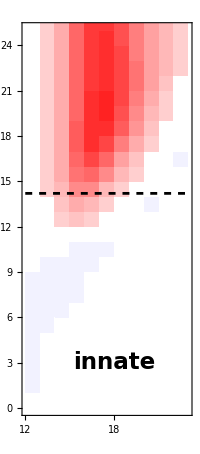

```mathematica
innateplot=Show[ Graphics[Table[Style[Rectangle[{totaldeltaPinnate[[i]][[1]],totaldeltaPinnate[[i]][[2]]},{totaldeltaPinnate[[i]][[1]]+50/partitiongrid,totaldeltaPinnate[[i]][[2]]+50/partitiongrid}], transformedcolorbefore[[i]], Opacity[1]], {i, 1, Length[totaldeltaPinnate[[All,3]]]}], (*PlotRange -> {{10, 35}, {0, 55}},*)PlotRange->{{12, 23}, {0, 25}}, Ticks-> None,Frame->True, FrameStyle->Directive[Black, Thick,Bold, 15],Epilog->Text[Style["innate", 23, Bold], Offset[{0,0}, {18,3}]],PlotRangeClipping->True],ListPlot[Table[{x,14.2},{x,12, 23}], Joined->True,PlotStyle->{Black, Dashed}]]
```

### Plot them together with the plot legend

```mathematica
mindensityb
```

-2122.62

```mathematica
Round[-2122.617755,50]/5
```

-420

```mathematica
N[Round[maxdensityb*.5, 50]/5000]
```

0.08

```mathematica
maxdensityb
```

847.042

```mathematica
N[Round[maxdensityb,10]/5000]
```

0.17

```mathematica
plotlegend2=BarLegend[{colordensityfunctionbefore,{mindensityb,maxdensityb}},"Ticks"->{{mindensityb,Round[-2122.617755,50]/5000},{-2000,-2000/5000},{Round[-2000*2/3,50],Round[-2000*2/3,50]/5000},{Round[-2000/3,50],Round[-2000/3,50]/5000},{0,0},{maxdensityb*.5,Round[maxdensityb*.5, 50]/5000},{maxdensityb,N[Round[maxdensityb*1.0,50]]/5000}},LegendLabel->"Δ P", LabelStyle->Directive[Bold, Medium, Black,15]]
```

```mathematica
(*plotlegend2=BarLegend[{colordensityfunctionbefore,{mindensityb,maxdensityb}},"Ticks"->{{mindensityb,Round[-2122.617755,50]},-2000,Round[-2000*2/3,50],Round[-2000/3,50],0,{maxdensityb*.5,Round[maxdensityb*.5, 50]},{maxdensityb,NumberForm[850, {5, 0}]}},LegendLabel->"Δ P", LabelStyle->Directive[Bold, Medium, Black,15]]*)
```

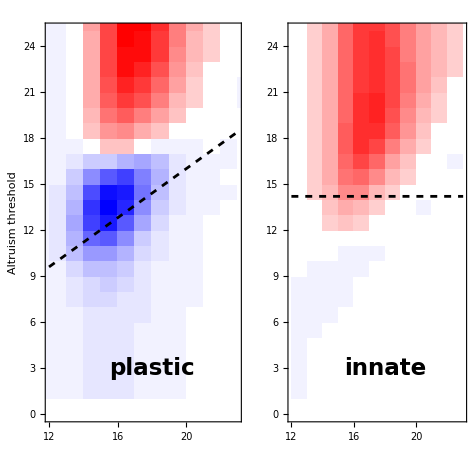

```mathematica
optimalfig=GraphicsRow[{plasticplot, innateplot, plotlegend2},ImageSize->475,Epilog->Text[Style["Average partner distance", 25, Bold], Offset[{0,0}, {215,-505}]], ImagePadding->{{Automatic, Automatic}, {25, Automatic}}]
```

```mathematica
optimalfig=GraphicsRow[{plasticplot, innateplot, plotlegend2},ImageSize->475,Epilog->Text[Style["Average partner distance", 25, Bold], Offset[{0,0}, {240,-432.5}]], ImagePadding->{{Automatic, Automatic}, {25, Automatic}}]
```

-Graphics-

```mathematica
currentdir=Directory[];
SetDirectory["~/Desktop"];
Export["fig3.pdf", optimalfig];
SetDirectory[currentdir];
```

## Figure 4 : Strategy State Space

### Invading Plastic

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data/"];
invadingplasticfrequencies=Import["fig4_frequencies_invadingplastic.txt","CSV"];
invadingplasticfrequencies=Transpose[{Flatten[Downsample[invadingplasticfrequencies, 3]], Flatten[Downsample[Drop[invadingplasticfrequencies, 1], 3]],Flatten[Downsample[Drop[invadingplasticfrequencies, 2], 3]]}];
SetDirectory[currentdir];
```

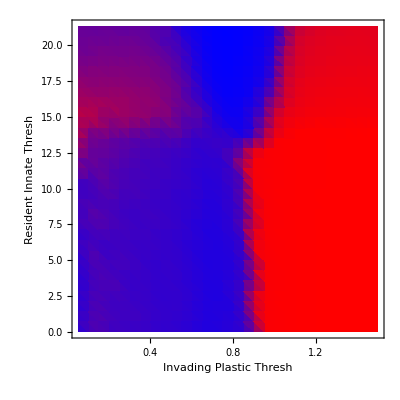

```mathematica
Tvafreq=ListDensityPlot[invadingplasticfrequencies, ColorFunction-> redtoblue,PlotLegends->None,PlotRange->All, FrameLabel -> {"Invading Plastic Thresh","Resident Innate Thresh"},FrameStyle->Directive[Black, 15, Thickness[.004]],LabelStyle -> {FontFamily->labelfont,Large, 15, Bold}]
```

```mathematica
currentdir=Directory[];
SetDirectory["~/Desktop"];
Export["supplement_fig4_invplastic.pdf", Tvafreq];
SetDirectory[currentdir];
```

### Resident Plastic

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data/"];
residentplasticfrequencies=Import["fig4_frequencies_residentplastic.txt","CSV"];
residentplasticfrequencies=Transpose[{Flatten[Downsample[residentplasticfrequencies, 3]], Flatten[Downsample[Drop[residentplasticfrequencies, 1], 3]],Flatten[Downsample[Drop[residentplasticfrequencies, 2], 3]]}];
SetDirectory[currentdir];
```

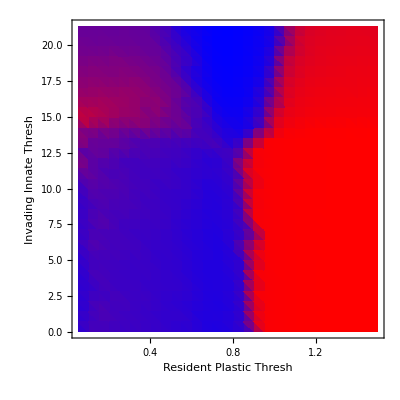

```mathematica
Tvafreq=ListDensityPlot[residentplasticfrequencies, ColorFunction-> redtoblue,PlotLegends->None(*BarLegend[Automatic,LegendLabel->"Freq. of Plastic"]*)(*{{Red, Blue}, {0,5000}}, LegendLabel->"Donations"]*),PlotRange->All, FrameLabel -> {"Resident Plastic Thresh","Invading Innate Thresh"},(*AxesStyle->Directive[Black,Bold, 15],TicksStyle -> Directive[Black, Thick, 22,FontFamily->labelfont],*) FrameStyle->Directive[Black, 15, Thickness[.004]],LabelStyle -> {FontFamily->labelfont,Large, 15, Bold}]
```

```mathematica
currentdir=Directory[];
SetDirectory["~/Desktop"];
Export["supplement_fig4_invinnate.pdf", Tvafreq];
SetDirectory[currentdir];
```

### Evolving coordinates

```mathematica
arrowgraphic=-Graphics-;
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data/"];
(*SetDirectory["~/Desktop"];*)
angle=Flatten[Import["fig4_evolvingcoords_angles.txt","CSV"]];
magnitudes=Flatten[Import["fig4_evolvingcoords_magnitudes.txt","CSV"]];
recenterdropnothings = Import["fig4_evolvingcoords_arroworigins.txt","CSV"];
recenterdropnothings=Transpose[{Flatten[Downsample[recenterdropnothings, 2]], Flatten[Downsample[Drop[recenterdropnothings, 1], 2]]}];
recenterdropnothings=Table[{recenterdropnothings[[i]], recenterdropnothings[[i+1]]}, {i, 1,  Length[recenterdropnothings],2}];
SetDirectory[currentdir];
```

```mathematica
biggest=Max[magnitudes];
```

```mathematica
arrows=Table[Graphics[Rotate[arrowgraphic,angle[[i]]],ImageSize->magnitudes[[i]]*30/biggest+15] ,{i, 1, Length[recenterdropnothings]}];
origins = Table[recenterdropnothings[[i]][[1]], {i, 1, Length[recenterdropnothings]}];
origins=Partition[origins,1];
```

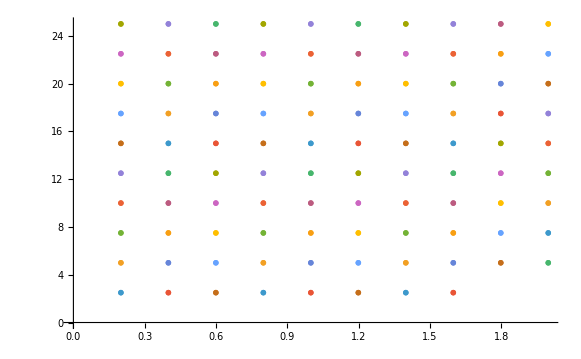

```mathematica
arrowplot=ListPlot[origins, PlotMarkers->arrows]
```

### Combine above

```mathematica
avfrequencies=Mean[{invadingplasticfrequencies,residentplasticfrequencies}];
lowerline = Graphics[{Thickness[0.0075],Dashed, White, Line[{{.7, 0}, {.7, 22}}]}];
upperline = Graphics[{Thickness[0.0075],Dashed, White, Line[{{.9, 0}, {.9, 22}}]}];
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data/"];
coords=Import["fig4_finalcoords.txt","CSV"];
coords = Transpose[{Flatten[Downsample[coords, 2]], Flatten[Downsample[Drop[coords, 1], 2]]}];
colors1 =Import["fig4_finalcoords_frequencies.txt", "CSV"];
SetDirectory[currentdir];
```

```mathematica
positions=Position[coords[[All,2]],x_/;x>=21];
```

```mathematica
inboundspos=Complement[Range[1,Length[coords]],Flatten[positions]];
```

```mathematica
coords1=coords[[inboundspos]];
colors1=colors1[[inboundspos]];
```

```mathematica
colors1=redtoblue/@Flatten[colors1];
rednblue=Show[ListPlot[coords1, PlotStyle->White,BaseStyle->{PointSize[.05]}],ListPlot[Partition[coords1,1], PlotStyle->colors1,BaseStyle->{PointSize[.03]}]];
```

```mathematica
oldplot=ListDensityPlot[avfrequencies, ColorFunction-> redtoblue,PlotLegends->None(*BarLegend[Automatic,LegendLabel->"Freq. of Plastic"]*)(*{{Red, Blue}, {0,5000}}, LegendLabel->"Donations"]*),PlotRange->All, FrameLabel -> {"Plastic a","Innate T"},(*AxesStyle->Directive[Black,Bold, 15],TicksStyle -> Directive[Black, Thick, 22,FontFamily->labelfont],*) FrameStyle->Directive[Black, 25, Thickness[.004]],LabelStyle -> {FontFamily->labelfont,Large, 15, Bold}, Epilog-> rednblue[[1]]];
```

```mathematica
thelegend=BarLegend[{{RGBColor[1,0,0], RGBColor[0,0,1]}, {0,1}}, LegendLabel->"Plastic Frequency", LabelStyle->Directive[Bold, Medium,20], TicksStyle->Black]
```

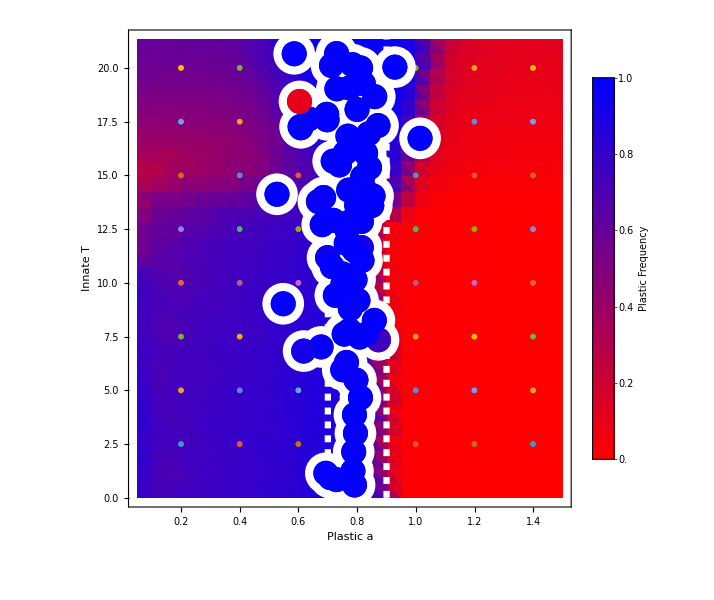

```mathematica
newplot=Show[oldplot, lowerline,upperline,arrowplot, ImageSize->600];
figthree=Legended[newplot, thelegend]
```

```mathematica
currentdir=Directory[];
SetDirectory["~/Desktop"];
Export["fig4.pdf", newplot];
SetDirectory[currentdir];
```

## Figure 5: 2-cluster regime

```mathematica
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/large_unprocessed_data"];
```

```mathematica
fitdat=Import["FITNESSES_Dim020_Pop1000_Gen10000000_B10.00_C1.00_PM1.0000_SM0.0010_ICthresh1000.00000_ICscaler0.65000_Tsigma0.50000_Ssigma0.01000_iteration1"];
```

```mathematica
fitdata=fitdat;
```

```mathematica
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
flatphenova=Import["fig5_flatphenova.csv"];
```

```mathematica
sampleofdata=Transpose[{Downsample[flatphenova[[All,1]],5], Downsample[flatphenova[[All,2]],5]}]
```

```mathematica
inverted = Transpose[{sampleofdata[[All,1]], sampleofdata[[All,2]]}];
```

```mathematica
Position[Drop[fitdat[[All,23]],1],Min[Drop[fitdat[[All,23]],1]]]
```

{{131092},{131309},{131485}}

```mathematica
N[131092/500]
```

262.184

```mathematica
j= 262
phenotypes1 = Table[Drop[fitdat[[All,i]],1][[1+500*j;;500*(j+1)]], {i,1, 20}];
```

262

```mathematica
phenotypes1=Transpose[phenotypes1];
```

```mathematica
Position[Drop[fitdat[[All,23]],1],Max[Drop[fitdat[[All,23]],1]]]
```

{{450356}}

```mathematica
N[450356/500]
```

900.712

```mathematica
j= 900;
phenotypes2 = Table[Drop[fitdat[[All,i]],1][[1+500*j;;500*(j+1)]], {i,1, 20}];
```

```mathematica
phenotypes2=Transpose[phenotypes2];
```

```mathematica
coords2=Transpose[{PrincipalComponents[phenotypes2,Method->"Covariance"][[All,1]],PrincipalComponents[phenotypes2,Method->"Covariance"][[All,2]]}];
```

```mathematica
coords1=Transpose[{PrincipalComponents[phenotypes1,Method->"Covariance"][[All,1]],PrincipalComponents[phenotypes1,Method->"Covariance"][[All,2]]}];
```

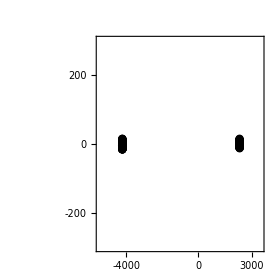

```mathematica
a2plot=ListPlot[coords2,PlotStyle-> Black,AxesStyle->{Bold,Black},FrameTicks-> {{{-200, 0,200},None},{{-4000, 0, 3000},None}},PlotMarkers->Graphics[{Black,Disk[{0,0}]}, ImageSize->8.5],LabelStyle -> {Bold,Black,20},PlotRange->{{-5500, 3500}, {-300, 300}}, Background-> White,FrameStyle-> 20,Frame->True,ImageSize-> 275, AspectRatio->1,Epilog->Text[Style[A,34,Bold,FontFamily->labelfont],Offset[{0,0},{-10000,350}]],PlotRangeClipping->False,ImagePadding->{{130, 30}, {25, 30}},FrameLabel-> {{None,None},{None,"2 Cluster PCA"}}]
```

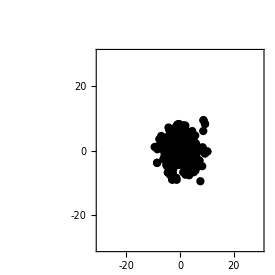

```mathematica
a1plot=ListPlot[coords1,PlotStyle-> Black,AxesStyle->{Bold,Black},FrameTicks-> {{{-20, 0,20},None},{{-20, 0, 20},None}},PlotMarkers->Graphics[{Black,Disk[{0,0}]}, ImageSize->8.5],LabelStyle -> {Bold,Black,20},PlotRange->{{-30, 30}, {-30, 30}},Background-> White,FrameStyle-> 20,Frame->True,ImageSize-> 275, AspectRatio->1,Epilog->Text[Style[B,34,Bold,FontFamily->labelfont],Offset[{0,0},{-55,38.5}]],PlotRangeClipping->False,ImagePadding->{{130, 30}, {25, 30}},FrameLabel-> {{None,None},{None,"1 Cluster PCA"}}]
```

```mathematica
img=Grid[{{a2plot,a1plot},{Null,Null}},Spacings->9]
```

-Graphics- | -Graphics-
 |

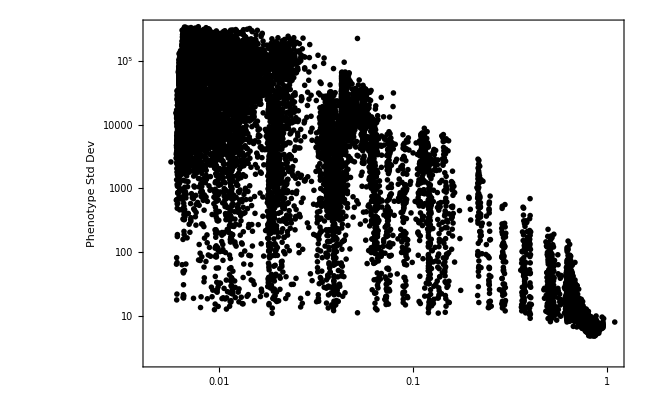

```mathematica
plots=ListLogLogPlot[inverted,AxesStyle->Directive[Black, 15],PlotMarkers->{"●",Scaled[.015]},PlotStyle-> Black,FrameTicksStyle->Directive[Black, 18, FontFamily-> labelfont],Ticks-> {Automatic,Automatic},ImageSize->650,ImagePadding->{{110,10},{30(*21*),5}},Frame-> True,FrameLabel->{None,"Phenotype Std Dev"}, 
RotateLabel->True,LabelStyle -> {FontFamily->labelfont,Black,Large, 22,Bold},FrameTicksStyle->Directive[Black, 16, FontFamily-> labelfont]]
```

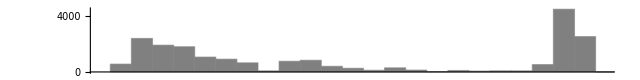
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
twocluster=Grid[{{Histogram[sampleofdata[[All,1]], {"Log",25},AspectRatio->1/8,ImageSize->640,ChartStyle-> Gray, Ticks->{None,{0,2000,4000}},TicksStyle-> 18,LabelStyle-> Bold,PlotRange->{{.0045,1.1},All},ImagePadding->{{110,0},{5,5}},Epilog->Text[Style[C,36,Bold,FontFamily-> labelfont],Offset[{0,0},{-6.35,3500}]]],Null}, {plots, Histogram[sampleofdata[[All,2]],{"Log",25},AspectRatio->4.75,ImageSize->100,ChartStyle-> Gray,BarOrigin-> Left,Ticks->{{1000,4000},None},PlotRange->{{0,4000},{2, 450000}}, ImagePadding->{{10,21.5},{30(*22*),10}},TicksStyle-> 18,LabelStyle-> Bold]}}, Alignment->{{Left,Left},{Left,Bottom}}]
```

### Change the threshold fig

```mathematica
scalersvthreshs = Transpose[{Drop[fitdat,1][[All,25]], Drop[fitdat,1][[All,28]]}];
```

```mathematica
dummycoords = Table[10^i, {i, -3, Log[10,.4], .15}];
```

```mathematica
lastcoords = Table[10^i, {i, Log[10,.4],0, .025}];
```

```mathematica
joinedcoords = {Flatten[Join[dummycoords,lastcoords]]};
```

```mathematica
joinedcoords
```

{{0.001,0.00141254,0.00199526,0.00281838,0.00398107,0.00562341,0.00794328,0.0112202,0.0158489,0.0223872,0.0316228,0.0446684,0.0630957,0.0891251,0.125893,0.177828,0.251189,0.354813,0.4,0.423701,0.448807,0.475401,0.50357,0.533409,0.565015,0.598494,0.633957,0.671522,0.711312,0.75346,0.798105,0.845396,0.895488,0.948549}}

```mathematica
list=Sort[scalersvthreshs, #1[[1]]<#2[[1]]&];
partitions=BinCounts[list[[All,1]],joinedcoords];
binnedcoords=TakeList[list,partitions];
```

```mathematica
coordswithbin = Transpose[{Drop[Flatten[joinedcoords],1], binnedcoords}];
```

```mathematica
coordswithbin=Drop[coordswithbin,1];
```

```mathematica
coords={};
For[ q = 1, q <= Length[coordswithbin], q++,
line=Table[If[Length[coordswithbin[[All,2]][[q]][[All,2]]]>500,{coordswithbin[[All,1]][[q]],coordswithbin[[All,2]][[q]][[All,2]][[j]]},
{coordswithbin[[All,1]][[q]],coordswithbin[[All,2]][[q]][[All,2]][[j]]}
], 
{j,If[Length[coordswithbin[[All,2]][[q]][[All,2]]]>500, RandomSample[Range[Length[coordswithbin[[All,2]][[q]][[All,2]]]],500],  Range[Length[coordswithbin[[All,2]][[q]][[All,2]]]]]}
];
AppendTo[coords, line];
]
```

```mathematica
coords = Drop[coords,1];
```

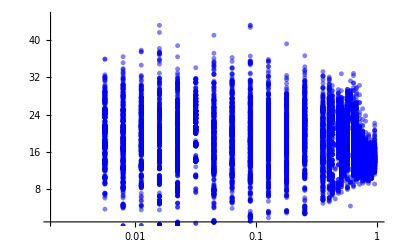

```mathematica
ListLogLinearPlot[Flatten[Drop[coords/.{}->Nothing,1],1],PlotRange-> {{.002, 1}, {1, 45}},PlotStyle->Directive[Black,18],AxesStyle->Directive[Black,Bold, 15],TicksStyle -> Directive[Black,Thick, 15, FontFamily-> labelfont],PlotMarkers->Table[Graphics[{Blue,Opacity[.5],Disk[{0,0},.5]},ImageSize->5] ,{i, 1, Length[coords]}] ]
```

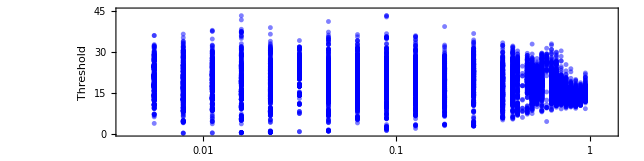

```mathematica
plotd=ListLogLinearPlot[Flatten[Drop[coords/.{}->Nothing,1],1],PlotRange->{{.004,1.25},{0, 45}},
PlotMarkers->Table[Graphics[{Blue,Opacity[.5],Disk[{0,0},.5]},ImageSize->5] ,{i, 1, Length[coords]}],
AxesStyle->Directive[Black, 15],
FrameTicksStyle->Directive[Black, 18, FontFamily-> labelfont],Ticks-> {Automatic,Automatic},ImageSize->644,ImagePadding->{{110,1},{65,1}},Frame-> True,FrameLabel->{"Threshold coefficient","Threshold"}, 
RotateLabel->True,LabelStyle -> {FontFamily->labelfont,Black,Large, 22,Bold},FrameTicksStyle->Directive[Black, 18, FontFamily-> labelfont],Epilog -> {Text[Style[D,34,Bold,FontFamily-> labelfont],Offset[{0,0},{-6.35,40}]]},
 AspectRatio->1.5/6,PlotRangeClipping->False ]
```

```mathematica
twoclusterplot=Column[{img,twocluster,plotd}]
```

-Graphics- | -Graphics-
 | 
-Graphics- | 
-Graphics- | -Graphics-
-Graphics-

```mathematica
currentdir=Directory[];
SetDirectory["~/Desktop"];
Export["fig5.pdf", twoclusterplot];
SetDirectory[currentdir];
```

## Supplement Figure : Robustness

### Vary SM

```mathematica
meanfreqnum=Import["supplement1_meanfreqnm_SM.txt","CSV"];
```

```mathematica
meanfreqnum=Transpose[{Flatten[Downsample[meanfreqnum, 3]], Flatten[Downsample[Drop[meanfreqnum, 1], 3]],Flatten[Downsample[Drop[meanfreqnum, 2], 3]]}];
```

```mathematica
allpts=Import["supplement1_allpts_SM.txt","CSV"];
```

```mathematica
allpts=Transpose[{Flatten[Downsample[allpts, 2]], Flatten[Downsample[Drop[allpts, 1], 2]]}];
```

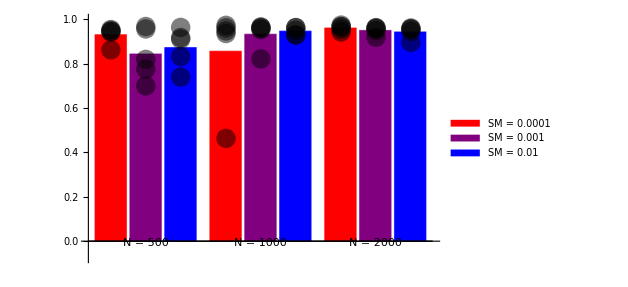

```mathematica
smplot=Show[BarChart[meanfreqnum,PlotRange->{All,{-.075, 1}},ChartLegends->{Style["SM = 0.0001",17.5],Style["SM = 0.001",17.5],Style["SM = 0.01",17.5]},ChartLabels->{{"N = 500","N = 1000","N = 2000"},None},ChartStyle->{Red, Purple, Blue},AxesStyle->{{Bold,Black,15},{Bold,Black,15}},(*AxesLabel->{None,"Frequency"},*)(*ImagePadding->30,*)ImagePadding-> {{130, 20}, {10, 12}},ImageSize->465,Epilog->Text[Style[A,27,Bold,FontFamily-> labelfont],Offset[{0,0},{-1.,1}]]],ListPlot[allpts, PlotStyle->{Black,Opacity[.5]}, PlotMarkers->{"●",20}]]
```

### Vary dimension

```mathematica
meanfreqnum=Import["supplement1_meanfreqnm_dim.txt","CSV"];
```

```mathematica
meanfreqnum=Transpose[{Flatten[Downsample[meanfreqnum, 3]], Flatten[Downsample[Drop[meanfreqnum, 1], 3]],Flatten[Downsample[Drop[meanfreqnum, 2], 3]]}];
```

```mathematica
allpts=Import["supplement1_allpts_dim.txt","CSV"];
```

```mathematica
allpts=Transpose[{Flatten[Downsample[allpts, 2]], Flatten[Downsample[Drop[allpts, 1], 2]]}];
```

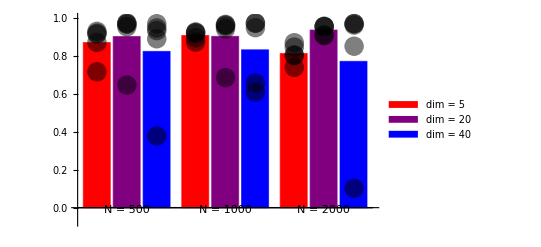
-Graphics-Plastic Frequency

```mathematica
newdimplot=Labeled[Show[BarChart[meanfreqnum,PlotRange->{All,{-.075, 1}},ChartLegends->{Style["dim = 5",17.5],Style["dim = 20",17.5],Style["dim = 40",17.5]}, ChartLabels->{{"N = 500","N = 1000","N = 2000"},None},ChartStyle->{Red, Purple, Blue},AxesStyle->{{Bold,Black,15},{Bold,Black,15}},AxesLabel->{None,None},ImageSize->400,ImagePadding-> {{65, 20}, {22, 22}},Epilog->Text[Style[B,27,Bold,FontFamily-> labelfont],Offset[{0,0},{-1.,1}]]],ListPlot[allpts, PlotStyle->{Black,Opacity[.5]}, PlotMarkers->{"●",20}]],"Plastic Frequency", {{Left, Center}}, RotateLabel->True,LabelStyle -> {FontFamily->labelfont,Large, 28, Bold}]
```

### Vary b/c

```mathematica
meanfreqnum=Import["supplement1_meanfreqnm_bc.txt","CSV"];
```

```mathematica
meanfreqnum=Transpose[{Flatten[Downsample[meanfreqnum, 3]], Flatten[Downsample[Drop[meanfreqnum, 1], 3]],Flatten[Downsample[Drop[meanfreqnum, 2], 3]]}];
```

```mathematica
allpts=Import["supplement1_allpts_bc.txt","CSV"];
```

```mathematica
allpts=Transpose[{Flatten[Downsample[allpts, 2]], Flatten[Downsample[Drop[allpts, 1], 2]]}];
```

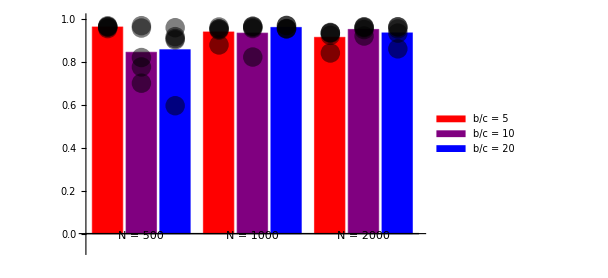

```mathematica
newbcplot=Show[BarChart[meanfreqnum,PlotRange->{All,{-.075, 1}},ChartLegends->{Style["b/c = 5",17.5],Style["b/c = 10",17.5],Style["b/c = 20",17.5]}, ChartLabels->{{"N = 500","N = 1000","N = 2000"},None},ChartStyle->{Red, Purple, Blue},AxesStyle->{{Bold,Black,15},{Bold,Black,15}},AxesLabel->{None,None},ImageSize->450,ImagePadding-> {{100, 20}, {10, 14}},Epilog->Text[Style[C,27,Bold,FontFamily-> labelfont],Offset[{0,0},{-1.,1}]]],ListPlot[allpts, PlotStyle->{Black,Opacity[.5]}, PlotMarkers->{"●",20}]]
```

### Put fig together

```mathematica
robustplot=GraphicsColumn[{smplot,newdimplot,newbcplot},Spacings->0, ImageSize->640]
```

-Graphics-

```mathematica
currentdir=Directory[];
SetDirectory["~/Desktop"];
Export["robustplot.pdf", robustplot]
SetDirectory[currentdir];
```

robustplot.pdf